```mathematica
Remove ["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Homework #3 problem 2 &5.

Problem 2

```mathematica
Fx = Log[1+x]
```

Log[1+x]

```mathematica
S0=Normal[Series[Fx, {x,2,0}]]
```

Log[3]

```mathematica
S1 = Normal[Series[Fx, {x,2,1}]]
```

1/3 (-2+x)+Log[3]

```mathematica
S2=Normal[Series[Fx, {x,2,2}]]
```

1/3 (-2+x)-1/18 (-2+x)^2+Log[3]

```mathematica
S3 =Normal[Series[Fx, {x,2,3}]]
```

1/3 (-2+x)-1/18 (-2+x)^2+1/81 (-2+x)^3+Log[3]

```mathematica
Plot[{Fx,S0,S1,S2,S3},{x,-1,1.5},PlotLabels->{function,zeroth order, first order, second order, third order}]
```

-Graphics-

Problem 5

```mathematica
x=4*Cos[((2*Pi)*t)]
```

4 Cos[2 π t]

```mathematica
x1=4*Cos[((2*Pi)*t)+(-Pi/4)]
```

4 Cos[π/4-2 π t]

```mathematica
x2=4*Cos[((2*Pi)*t)+(Pi/4)]
```

4 Cos[π/4+2 π t]

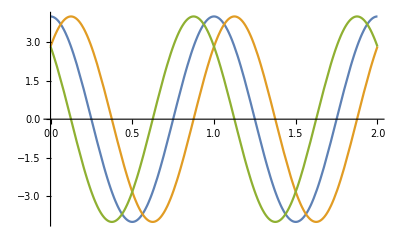

```mathematica
Plot[{x,x1,x2},{t,0,2}]
```